```mathematica
LIMITA FUNKCIJE
```

Limita funkcije v točki a je število, ki se mu vrednost funkcije  f(x) približuje, ko se vrednost spremenljivke x približuje danemu številu a. Število a je v definicijskem območju ali vsaj na njegovem
robu.  Limito funkcije označimo z f(x)xa  (beri: " Limita f(x), ko gre x proti a."). 
Dodatno definiramo za funkcijo f(x) z navzgor neomejenim definicijskim območjem. 
A  =  f(x)xa ⟺ f(x)  se od števila A loči za poljubno malo za vsak dovolj velik x ϵ Df.

```mathematica
Računanje limit funkcij ene spremenljivke:

Če ostajata f(x)xa in g(x)xa (za a ∈ ℝ ali a = ±∞),  je : 

≻[f(x) xa± g(x)] = f(x)xa ± g(x)xa
≻cf(x)xa = c  · f(x)xa
≻f(x)g(x) = xaf(x)xa · g(x)xa 
≻g(x)xa ≠ 0 ⇒ (f(x))/(g(x))xa = (f(x)xa)/(g(x)xa)
≻(f(x))^nxa = [(f(x)])^nxa       (f(x))^(1/n)xa = (f(x)xa)^(1/n)
≻c^(f(x))xa = c^(f(x)xa)
≻h(f(x)) = h(f(x)) xaxa za vsako zvezno funkcijo h.
```

Zgled: 
(a) (x^2-1)/(x-1)x1 = (x+1)x1 = 2
(b)(√(x+2)-2)/(x-2)x2 = 1/(√(x+2)+2)x2 = 1/4
(c)  (1-cosx)/x^2x0 = (sin^2 x)/(x^2 (1+cosx))x0 = 1/2

Limita v neskončnosti

Pri funkcijah ene realne spremenljivke nas včasih zanima, kako se vedejo funkcijske vrednosti, kadar argument x narašča ( ali pada ) preko vsake meje. Tedaj rečemo, da nas zanima limita funkcije v neskončnosti.

Zgled:

(a) (1-x)/(1+x)x±∞ = -1. Premica y = -1 je tedaj vodoravna asimptota funkcije f(x)= (1-x)/(1+x).
(b) Zgodi se, da sta leva in desna asimptota (pri pogojih x ⟶ -∞ in x ⟶ ∞) različni.
        Tako je npr. pri funkciji f(x) = arctgx ali npr. pri funkciji f(x) =ⅇ^x/(ⅇ^x+1) . V tem primeru je f(x)x-∞ = 0 in f(x)x∞ = 1.

Primeri limit:
1.

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞]
```

2/5

```mathematica
2.
```

```mathematica
Limit[(x^3-1)/(x-1),x->1]
```

3

```mathematica
3.
```

```mathematica
Limit[Sin[3x]/Tan[5x], x -> 0]
```

3/5

```mathematica
4.
```

```mathematica
Limit[(1-(x-1)^(1/3))/(2x-4), x->2]
```

-1/6

```mathematica
5.
```

```mathematica
Limit[(1+1/x)^(3x),x->Infinity]
```

ⅇ^3

```mathematica
6.
```

```mathematica
Limit[(x^2-1)/(x-1), x -> 0]
```

1

Primer limit funkcij:

```mathematica
Plot[(x^(1000)-1)/(x-1), {x, -2, 2}]
```

```mathematica
-Graphics-
Limit[(x^(1000)-1)/(x-1), x -> 0]
```

1

```mathematica
Plot[((x^3 + 3x +1)/(x-4)) + 1, {x, -1, 1}, Epilog->{PointSize[Large]}]
```

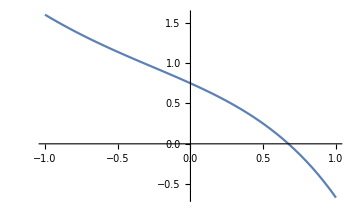
```mathematica
-Graphics-
Limit[((x^3 + 3x +1)/(x-4)) + 1, x -> 0]
```

3/4

```mathematica
Plot[Sin[x]+1/x, {x, -1,1}]
```

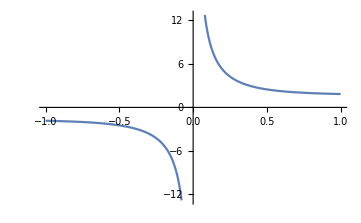
```mathematica
-Graphics-
Limit[Sin[x]+1/x,x->∞]
```

Indeterminate

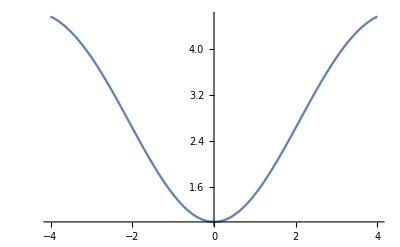

```mathematica
Plot[(-3 Sin[x]/x)+4, {x,-4, 4}]
```

```mathematica
Limit[(-3 Sin[x]/x)+4, x-> ∞]
```

4

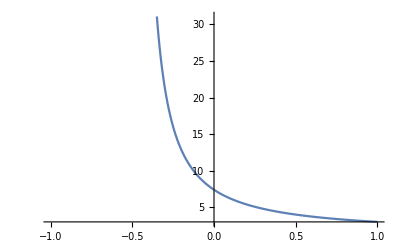

```mathematica
Plot[(1+2x)^(1/x), {x, -1, 1}]
```

```mathematica
Limit[(1+2 x)^(1/x),x->0]
```

ⅇ^2

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Limit[Sin[x+y^2], x-> ∞]
```

Interval[{-1,1}]

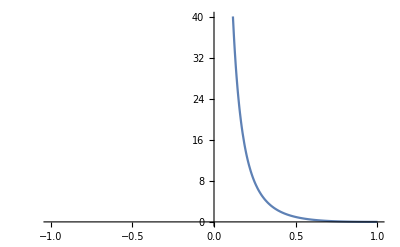

```mathematica
Plot[Log[x]^2/x, {x, -1, 1}]
```

```mathematica
Limit[Log[x]^2/x, x-> ∞]
```

0

```mathematica
Plot3D[sinx/(π^2-ℼ^2),{sinx,-8,8},{ℼ,-8,8}]
```

-Graphics3D-

```mathematica
Limit[(sinx/(x^2-ℼ^2)), x-> π]
```

sinx/(π^2-ℼ^2)

```mathematica
Limit[Sin[x]/x,x->0]
```

1

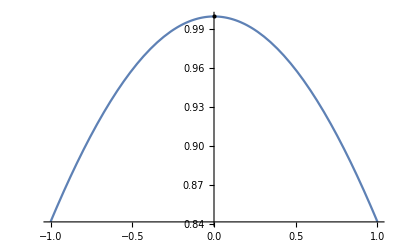

```mathematica
Plot[Sin[x]/x,{x,-1,1},Epilog->{PointSize[Large],Point[{0,1}]}]
```